# Thermal Expansion Coefficient

In this notebook we carry out the analysis of the thermal expansion coefficient for CSH .  Note: our refitted MLFF model is not suited for this calculations. The temperature blows up. Instead, I used the original one.

## Loading the data

```mathematica
wrdir= "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/thermal-exp/"
```

/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/thermal-exp/

```mathematica
SetDirectory[wrdir]
```

/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/thermal-exp

```mathematica
avgCellData = Import["lattice_averages.dat", "CSV"]
```

{{# Temp,Volume (A^3),LatVec1 (A),LatVec2 (A),LatVec3 (A),AvgLatVec (A)},{200,7366.97,13.0817,29.203,23.2809,21.8552},{250,7389.6,13.0759,29.2513,23.3014,21.8762},{300,7398.58,13.167,29.2864,23.1482,21.8672},{350,7425.,13.177,29.3256,23.1138,21.8722},{400,7467.37,13.3117,29.4787,23.1659,21.9854}}

```mathematica
tempData = avgCellData[[2;;,1]]
```

{200,250,300,350,400}

```mathematica
volData = avgCellData[[2;;,2]]
```

{7366.97,7389.6,7398.58,7425.,7467.37}

```mathematica
lattData = avgCellData[[2;;,6]]
```

{21.8552,21.8762,21.8672,21.8722,21.9854}

## Thermal expansion using the volume

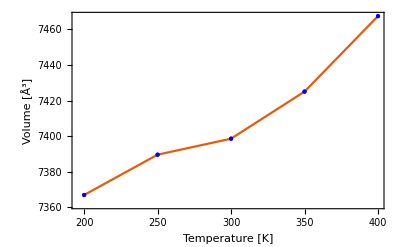

```mathematica
avgVolPlot=ListPlot[
Transpose[{tempData,volData}],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"Temperature [K]", "Volume [Å^3]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

### Thermal expansion coefficient

```mathematica
alphaV = 1/volData[[3]] (volData[[3]]-volData[[1]])/(tempData[[3]]-tempData[[1]])
```

0.0000427269

```mathematica
ScientificForm[alphaV]
```

4.27269×10^-5

## Thermal expansion using the lattice parameters

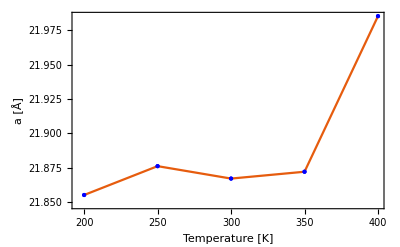

```mathematica
avgLattPlot=ListPlot[
Transpose[{tempData,lattData}],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"Temperature [K]", "a [Å]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

### Thermal expansion coefficient

```mathematica
alphaA = 1/lattData[[3]] (lattData[[3]]-lattData[[1]])/(tempData[[3]]-tempData[[1]])
```

5.46938×10^-6

```mathematica
ScientificForm[alphaA]
```

5.46938×10^-6